# Limb - darkening models - integral over halfsphere

Author : Martin Horvat, July 2016

### Logarithmic

```mathematica
Simplify[
2*Pi*Integrate[
(1-x*(1-Cos[theta])-y*Cos[theta]*Log[Cos[theta]])*Cos[theta] Sin[theta],{theta,0,Pi/2}]
]
```

1/9 π (9-3 x+2 y)

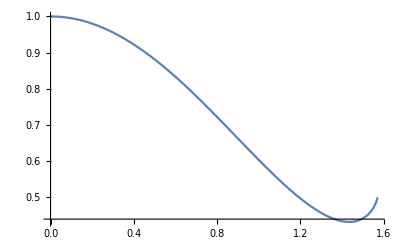

```mathematica
Plot[(1-x*(1-Cos[theta])-y*Cos[theta]*Log[Cos[theta]])/.{x->0.5,y->-0.5},{theta,0,Pi/2},PlotRange->All]
```

```mathematica
Minimize[{1-x*(1-u)-y*u*Log[u],1>u>0},u]
```

Minimize[{1-(1-u) x-u y Log[u],1>u>0},u]

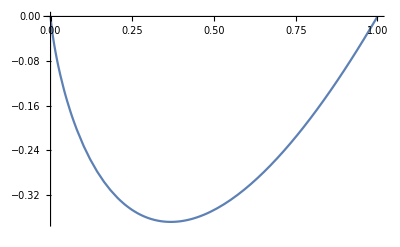

```mathematica
Plot[u Log[u],{u,0,1}]
```

### Nonlinear

```mathematica
Simplify[
2*Pi*Integrate[
(1-x*(1-Cos[theta])-y*(1-Cos[theta])^p)*Cos[theta] Sin[theta],{theta,0,Pi/2},Assumptions->p>1]
]
```

π (1-x/3-(2 y)/(2+3 p+p^2))

```mathematica
Minimize[{1-x u - y u^3,1>u>0},u]
```

{Piecewise[{{1, (y==0&&x==0)||(y==0&&x<0)||(y>0&&x≤-y)||(y<0&&x≤0)}, {1-x, y==0&&x>0}, {1/9 (9-2 √3 √(-x^3/y)), (y<0&&x==-3 y)||(y<0&&0<x<-3 y)}, {1-x-y, True}}],{u→Piecewise[{{1/2, y==0&&x==0}, {Indeterminate, (y==0&&x>0)||(y==0&&x<0)||(y>0&&x>-y)||(y>0&&x≤-y)||(y<0&&x==-3 y)||(y<0&&x>-3 y)||(y<0&&x≤0)}, {Root[-2 √3 √(-x^3/y)+9 x #1+9 y #1^3&,2], True}}]}}

### Quadratic

```mathematica
Simplify[
2*Pi*Integrate[
(1-x*(1-Cos[theta])-y*(1-Cos[theta])^2)*Cos[theta] Sin[theta],{theta,0,Pi/2}]
]
```

-1/6 π (-6+2 x+y)

```mathematica
Minimize[{1-x u - y u^2,1>u>0},u]
```

{Piecewise[{{1, (y==0&&x==0)||(y==0&&x<0)||(y>0&&x≤-y)||(y<0&&x≤0)}, {1-x, y==0&&x>0}, {1-x-y, (y>0&&x>-y)||(y<0&&x>-2 y)}, {(x^2+4 y)/(4 y), True}}],{u→Piecewise[{{1/2, y==0&&x==0}, {Indeterminate, (y==0&&x>0)||(y==0&&x<0)||(y>0&&x>-y)||(y>0&&x≤-y)||(y<0&&x==-2 y)||(y<0&&x>-2 y)||(y<0&&x≤0)}, {-x/(2 y), True}}]}}

### Linear

```mathematica
Simplify[
2*Pi*Integrate[
(1-x*(1-Cos[theta]))*Cos[theta] Sin[theta],{theta,0,Pi/2}]
]
```

π-(π x)/3

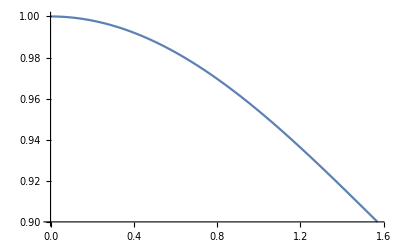

```mathematica
Plot[(1-x*(1-Cos[theta]))/.{x->0.1},{theta,0,Pi/2},PlotRange->All]
```

### Sqrt-root

```mathematica
Simplify[
2*Pi*Integrate[
(1-x*(1-Cos[theta])-y*(1-Sqrt[Cos[theta]]))*Cos[theta] Sin[theta],{theta,0,Pi/2}]
]
```

π (1-x/3-y/5)

### Uniform

```mathematica
Simplify[
2*Pi*Integrate[
1*Cos[theta] Sin[theta],{theta,0,Pi/2}]
]
```

π